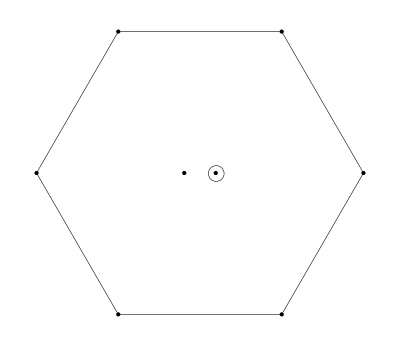

Y=0,  I_3=0

(ud-du)(d̄ū-ūd̄)+2(ds-sd)(d̄s̄-s̄d̄)+(us-su)(s̄ū-ūs̄)

```mathematica
(*-------------------------------*)
```

The current J:

(d_a^T Cγ^μ.(γ̄)^5 u_b-u_a^T Cγ^μ.(γ̄)^5 d_b) ((d̄)_a γ^μ.(γ̄)^5C((ū)_b)^T)+(d_a^T C γ^μ u_b-u_a^T C γ^μ d_b) ((d̄)_a γ^μ C((ū)_b)^T)+2 (s_a^T Cγ^μ.(γ̄)^5 d_b) ((d̄)_a γ^μ.(γ̄)^5C((s̄)_b)^T-(d̄)_b γ^μ.(γ̄)^5C((s̄)_a)^T)+(d_a^T C γ^μ u_b-u_a^T C γ^μ d_b) ((d̄)_b γ^μ C((ū)_a)^T)+2 (d_a^T Cγ^μ.(γ̄)^5 s_b-s_a^T Cγ^μ.(γ̄)^5 d_b) ((s̄)_a γ^μ.(γ̄)^5C((d̄)_b)^T)+(s_a^T Cγ^μ.(γ̄)^5 u_b-u_a^T Cγ^μ.(γ̄)^5 s_b) ((s̄)_a γ^μ.(γ̄)^5C((ū)_b)^T)+2 (s_a^T C γ^μ d_b) ((d̄)_a γ^μ C((s̄)_b)^T-(s̄)_a γ^μ C((d̄)_b)^T)+2 (d_a^T C γ^μ s_b) ((s̄)_a γ^μ C((d̄)_b)^T-(d̄)_a γ^μ C((s̄)_b)^T)+(s_a^T C γ^μ u_b-u_a^T C γ^μ s_b) ((s̄)_a γ^μ C((ū)_b)^T)+2 (d_a^T Cγ^μ.(γ̄)^5 s_b) ((d̄)_b γ^μ.(γ̄)^5C((s̄)_a)^T-(s̄)_b γ^μ.(γ̄)^5C((d̄)_a)^T)+2 (s_a^T C γ^μ d_b) ((d̄)_b γ^μ C((s̄)_a)^T-(s̄)_b γ^μ C((d̄)_a)^T)+2 (d_a^T C γ^μ s_b) ((s̄)_b γ^μ C((d̄)_a)^T-(d̄)_b γ^μ C((s̄)_a)^T)+(s_a^T C γ^μ u_b-u_a^T C γ^μ s_b) ((s̄)_b γ^μ C((ū)_a)^T)+(u_a^T Cγ^μ.(γ̄)^5 d_b-d_a^T Cγ^μ.(γ̄)^5 u_b) ((ū)_a γ^μ.(γ̄)^5C((d̄)_b)^T)+(u_a^T Cγ^μ.(γ̄)^5 s_b-s_a^T Cγ^μ.(γ̄)^5 u_b) ((ū)_a γ^μ.(γ̄)^5C((s̄)_b)^T)+(u_a^T C γ^μ d_b-d_a^T C γ^μ u_b) ((ū)_a γ^μ C((d̄)_b)^T)+(u_a^T C γ^μ s_b-s_a^T C γ^μ u_b) ((ū)_a γ^μ C((s̄)_b)^T)+(u_a^T Cγ^μ.(γ̄)^5 d_b) ((d̄)_b γ^μ.(γ̄)^5C((ū)_a)^T-(ū)_b γ^μ.(γ̄)^5C((d̄)_a)^T)+(d_a^T Cγ^μ.(γ̄)^5 u_b) ((ū)_b γ^μ.(γ̄)^5C((d̄)_a)^T-(d̄)_b γ^μ.(γ̄)^5C((ū)_a)^T)+(u_a^T Cγ^μ.(γ̄)^5 s_b) ((s̄)_b γ^μ.(γ̄)^5C((ū)_a)^T-(ū)_b γ^μ.(γ̄)^5C((s̄)_a)^T)+(s_a^T Cγ^μ.(γ̄)^5 u_b) ((ū)_b γ^μ.(γ̄)^5C((s̄)_a)^T-(s̄)_b γ^μ.(γ̄)^5C((ū)_a)^T)+(u_a^T C γ^μ d_b-d_a^T C γ^μ u_b) ((ū)_b γ^μ C((d̄)_a)^T)+(u_a^T C γ^μ s_b-s_a^T C γ^μ u_b) ((ū)_b γ^μ C((s̄)_a)^T)-2 (d_a^T Cγ^μ.(γ̄)^5 s_b(d̄)_a γ^μ.(γ̄)^5C((s̄)_b)^T)+2 (s_a^T Cγ^μ.(γ̄)^5 d_b(s̄)_b γ^μ.(γ̄)^5C((d̄)_a)^T)

the Fierz rearranged J (to naively get the decay partten)

```mathematica
-16 (d̄(γ̄)^5 s s̄(γ̄)^5 d)+8 (d̄(γ̄)^5 d) (2 (s̄(γ̄)^5 s)-ū(γ̄)^5 u)+8 (d̄ 1d) (ū 1u-2 (s̄ 1s))+16 (d̄ 1s s̄ 1d)+8 (d̄(γ̄)^5 u ū(γ̄)^5 d)-8 (d̄ 1u ū 1d)-8 (s̄(γ̄)^5 s ū(γ̄)^5 u)+8 (s̄(γ̄)^5 u ū(γ̄)^5 s)+8 (s̄ 1s ū 1u)-8 (s̄ 1u ū 1s)
```

Π(q^2)=
(53 g_s^2 log^2(-q^2/μ^2) q^8)/(5760 π^8)-(3 log(-q^2/μ^2) q^8)/(160 π^6)-(260399 g_s^2 log(-q^2/μ^2) q^8)/(2419200 π^8)-(3 ⟨ GG ⟩ log(-q^2/μ^2) q^4)/(2 π^5)+(⟨ ū u⟩ log(-q^2/μ^2) (m_d+m_s-6 m_u) q^4)/(3 π^4)+(⟨ s̄ s⟩ log(-q^2/μ^2) (4 m_d-15 m_s+m_u) q^4)/(3 π^4)+(⟨ d̄ d⟩ log(-q^2/μ^2) (-15 m_d+4 m_s+m_u) q^4)/(3 π^4)-(120 ⟨ d̄ d⟩^2 log(-q^2/μ^2) q^2)/π^2-(120 ⟨ s̄ s⟩^2 log(-q^2/μ^2) q^2)/π^2-(48 ⟨ ū u⟩^2 log(-q^2/μ^2) q^2)/π^2+(11 ⟨G^3⟩ log(-q^2/μ^2) q^2)/(6 π^6)-(176 ⟨ d̄ d⟩ ⟨ s̄ s⟩ log(-q^2/μ^2) q^2)/(3 π^2)+(280 ⟨ d̄ d⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/(3 π^2)+(280 ⟨ s̄ s⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/(3 π^2)-(64 ⟨ s̄ s⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(9 π^2)-(16 ⟨ ū u⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(9 π^2)-(64 ⟨ d̄ d⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(9 π^2)-(16 ⟨ ū u⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(9 π^2)-(16 ⟨ d̄ d⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(9 π^2)-(16 ⟨ s̄ s⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(9 π^2)-(40 ⟨ GG ⟩ ⟨ d̄ d⟩^2)/(π q^2)-(40 ⟨ GG ⟩ ⟨ s̄ s⟩^2)/(π q^2)-(16 ⟨ GG ⟩ ⟨ ū u⟩^2)/(π q^2)-(176 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ s̄ s⟩)/(9 π q^2)+(280 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ ū u⟩)/(9 π q^2)+(280 ⟨ GG ⟩ ⟨ s̄ s⟩ ⟨ ū u⟩)/(9 π q^2)+(4 ⟨ d̄ Gd⟩ ⟨ s̄ Gs⟩)/(3 π^2 q^2)+(⟨ d̄ Gd⟩ ⟨ ū Gu⟩)/(3 π^2 q^2)+(⟨ s̄ Gs⟩ ⟨ ū Gu⟩)/(3 π^2 q^2)-(128 ⟨ d̄ d⟩ ⟨ s̄ s⟩^2 (42 m_d+m_s))/(9 q^2)-(128 ⟨ d̄ d⟩^2 ⟨ s̄ s⟩ (m_d+42 m_s))/(9 q^2)+(384 ⟨ d̄ d⟩ ⟨ s̄ s⟩ ⟨ ū u⟩ (2 m_d+2 m_s-m_u))/q^2-(32 ⟨ d̄ d⟩ ⟨ ū u⟩^2 (42 m_d+m_u))/(9 q^2)-(32 ⟨ s̄ s⟩ ⟨ ū u⟩^2 (42 m_s+m_u))/(9 q^2)-(32 ⟨ d̄ d⟩^2 ⟨ ū u⟩ (m_d+42 m_u))/(9 q^2)-(32 ⟨ s̄ s⟩^2 ⟨ ū u⟩ (m_s+42 m_u))/(9 q^2)

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for η_6=η_8=η_10=1

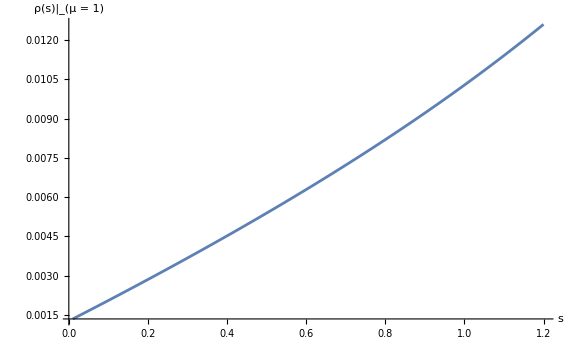
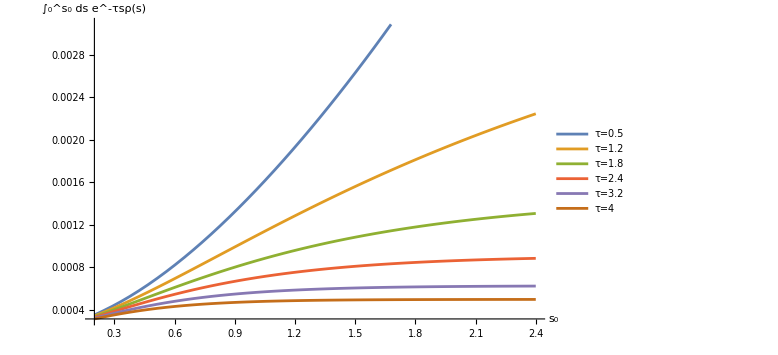

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for η_6=η_8=η_10=1

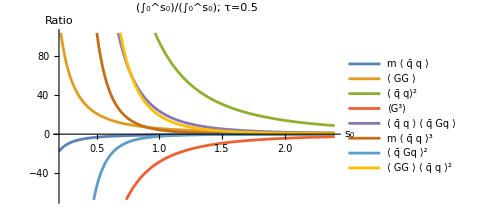
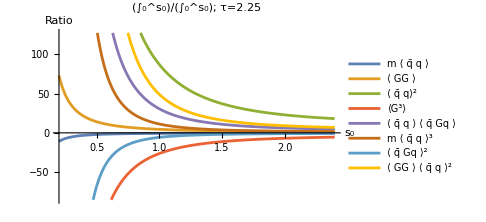
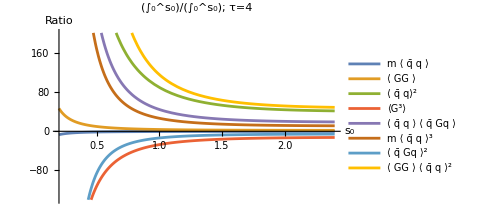

```mathematica
(*-------------------------------*)
```

ℛ^0 for η_6=η_8=η_10=1

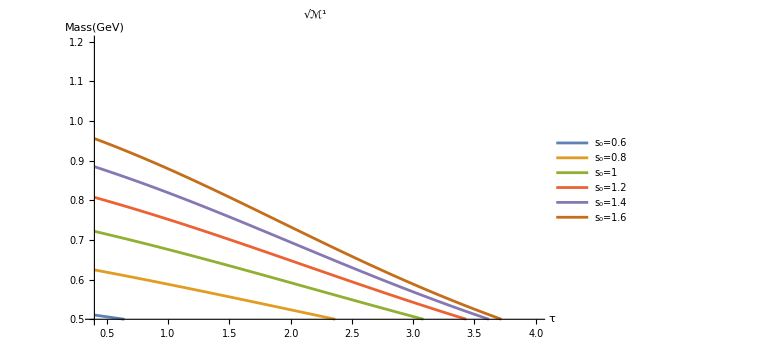
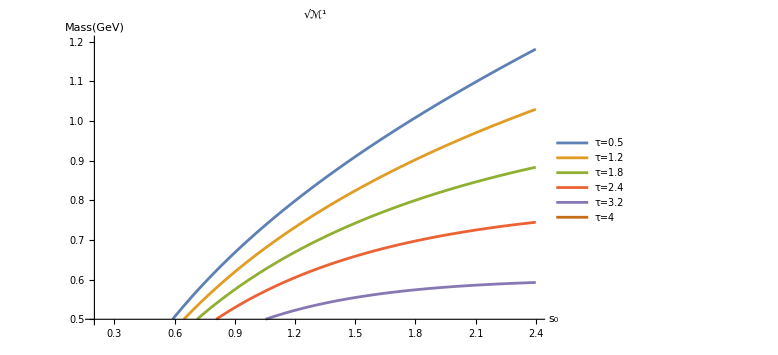

```mathematica
(*-------------------------------*)
```

ℛ^1 for η_6=η_8=η_10=1

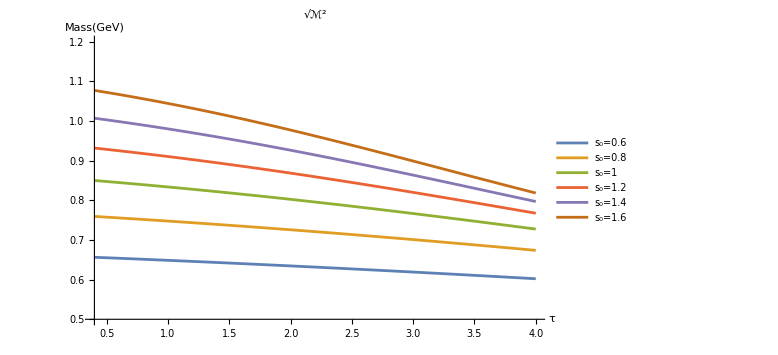
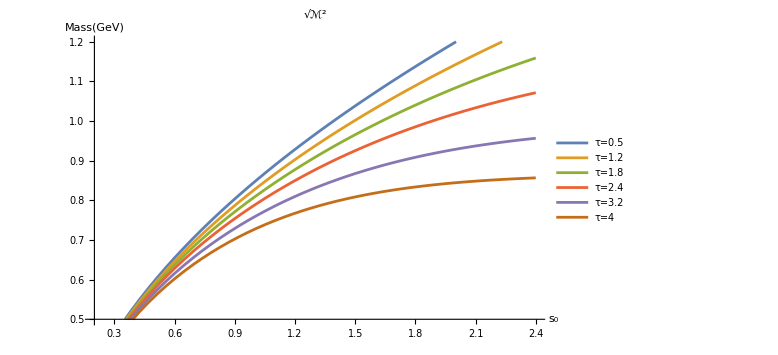

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for η_6=3, η_8=5, η_10=5

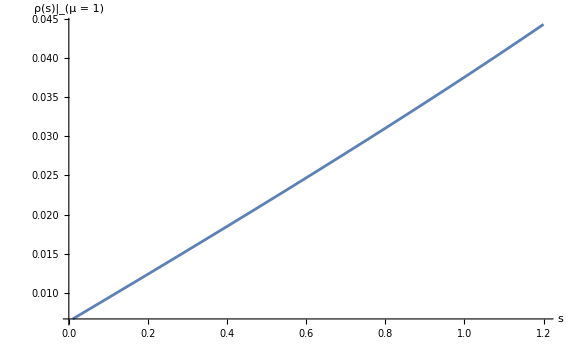
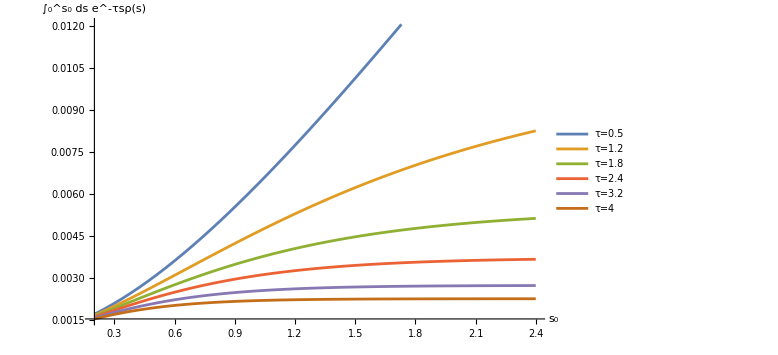

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for η_6=3, η_8=5, η_10=5

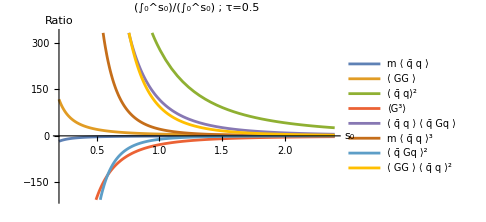
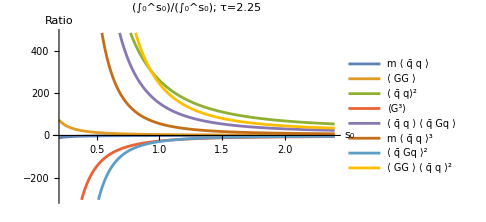
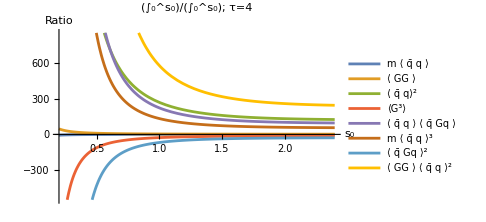

```mathematica
(*-------------------------------*)
```

ℛ^0 for η_6=3, η_8=5, η_10=5

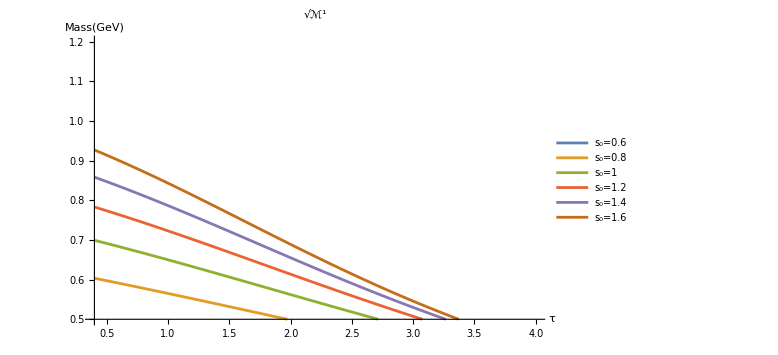
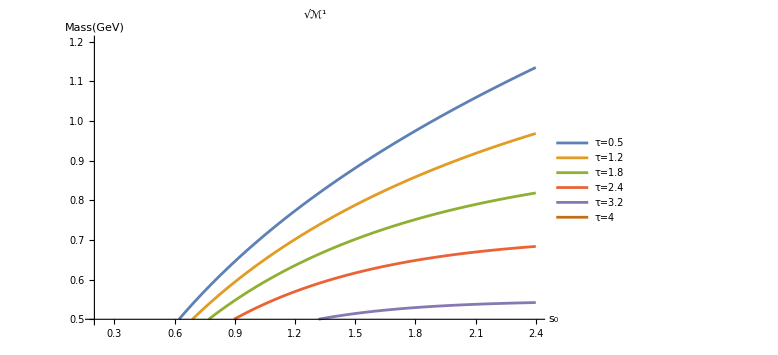

```mathematica
(*-------------------------------*)
```

ℛ^1 for η_6=3, η_8=5, η_10=5